```mathematica
f=n*Log[1+a]+n*Log[1+b]+a*Log[Pixi]+b*Log[Piyi]
```

n Log[1+a]+n Log[1+b]+a Log[Pixi]+b Log[Piyi]

```mathematica
D[f,{a,2}] (*求导*)
```

-n/(1+a)^2

```mathematica
Solve[n/(1+a)+Log[Pixi]==0,a] (*解方程*)
```

{{a→(-n-Log[Pixi])/Log[Pixi]}}

```mathematica
FullSimplify[%] (*化简*)
```

-n/(1+a)^2

```mathematica
f=2.56-3.85x^2+5.06*x^4
```

```mathematica
2.56-3.85 x^2+5.06 x^4
```

2.56-3.85 x^2+5.06 x^4

```mathematica
FindMaximum[{f,-1≤x≤1},{x,-1}] (*找局部最优解，要找到局部，但是不一定对*)
```

{3.77,{x→-1.}}

```mathematica
MaxValue[{f,-1≤x≤1},x] (*找全局最优解，记住格式第一个大括号里是范围，第二个是变量*)
```

3.77

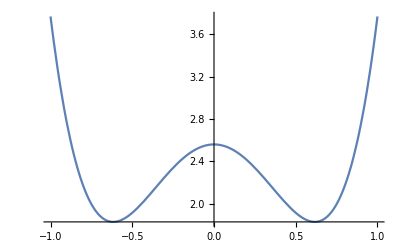

```mathematica
Plot[f,{x,-1,1}] (*画图范围*)
```

```mathematica
PDF[MultinomialDistribution[3,{1/2,1/3,1/6}],{x,y,z}]
```

Piecewise[{{2^(-x-z) 3^(-y-z) Binomial[3,z] Binomial[x+y,y], x+y+z==3&&x≥0&&y≥0&&z≥0}, {0, True}}]

ProbabilityDistribution::argmu: ProbabilityDistribution called with 1 argument; 2 or more arguments are expected.

ProbabilityDistribution[MultinomialDistribution[3,{1/2,1/3,1/6}]]

```mathematica
Mean[MultinomialDistribution[3,{1/2,1/3,1/6}]]
```

{3/2,1,1/2}

```mathematica
Covariance[MultinomialDistribution[n,{Subscript[p,1],Subscript[p,2]}]]//MatrixForm
```

(n (p_1-p_1^2) | -n p_1 p_2
-n p_1 p_2 | n (p_2-p_2^2))

```mathematica
MatrixForm[Covariance[MultinomialDistribution[3,{1/2,1/3,1/6}]]]
```

(3/4 | -1/2 | -1/4
-1/2 | 2/3 | -1/6
-1/4 | -1/6 | 5/12)

```mathematica
Table[DiscretePlot3D[PDF[MultinomialDistribution[3,{1/2,1/3,1/6}]],{x,y}],{y,0,n},{x,0,n},PlotLabel->Row[{"n = ",n}],ExtentSize->0.5]
```

Table::nliter: Non-list iterator PlotLabel→n =  at position 4 does not evaluate to a real numeric value.

Table[DiscretePlot3D[PDF[MultinomialDistribution[3,{1/2,1/3,1/6}]],{x,y}],{y,0,n},{x,0,n},PlotLabel→n = n,ExtentSize→0.5]

```mathematica
a={{1,-1/3}}
```

{{1,-1/3}}

```mathematica
b={{-1/3,0},{0,1}}
```

{{-1/3,0},{0,1}}

```mathematica
c={{1},{3}}
```

{{1},{3}}

```mathematica
Dot[a,b,c]
```

```mathematica
a=({{1, 1}, {-sin[z], sin[z]}});
b=({{1/2, 0}, {0, 1/2}});
c=({{1, -sin[z]}, {1, sin[z]}});
```

```mathematica
MatrixForm[a.b.c]
```

(1 | 0
0 | sin[z]^2)

```mathematica
MatrixForm[Inverse[a.b.c] ]
```

(1 | 0
0 | 1)

```mathematica
Det[{{1, -1/3}, {-1/3, 1}}]
```

8/9

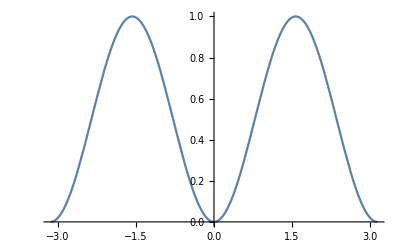

```mathematica
Plot[(Sin[x])^2,{x,-Pi,Pi}]
```

```mathematica
To create new rows=ctrl+enter,to create new cols=ctrl+,
```

```mathematica
a=({{1, 4, 6}})
b=({{6.859102, -0.445975969, -1.079557001}, {-0.445976, 0.161895369, -0.009155426}, {-1.079557, -0.009155426, 0.218577990}});
c=({{1}, {4}, {6}});
```

{{1,4,6}}

```mathematica
MatrixForm[a.b.c]
```

```mathematica
a=({{1, 150}})
```

{{1,150}}

```mathematica
b=({{3.40336672, -0.0207018689}, {-0.0207018689, 0.0001263111}});
c=({{1}, {150}})
```

{{1},{150}}

{{1,1},{1,1}}

```mathematica
a.b.c
```

```mathematica
{{0.03480580000000011}}
```

{{0.0348058}}

```mathematica
(*求导*)
f[t_]=(x/x-t)^20
```

(1-t)^20

(1-t)^20

```mathematica
D[(lambda/(lambda-t))^20,{t,2}]
```

```mathematica
(420 lambda^20)/(lambda-t)^22
(*积分*)
```

```mathematica
Integrate[(Cos[x]^2-Sin[x])/Cos[x]/(1+Cos[x] E^Sin[x]),x]
```

```mathematica
Log[Cos[x] Sec[x/2]^2]-Log[(1+ⅇ^Sin[x] Cos[x]) Sec[x/2]^2]+Sin[x]
```

Log[Cos[x] Sec[x/2]^2]-Log[(1+ⅇ^Sin[x] Cos[x]) Sec[x/2]^2]+Sin[x]

```mathematica
FullSimplify[D[(1-theta)*E^t/(1-theta*E^t),{t,2}]]
```

(ⅇ^t (-1+theta) (1+ⅇ^t theta))/((-1+ⅇ^t theta)^3)